```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pwrzosek/Documents/GitHub/Direct_Greens_Function/rotsaw/mathematica

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,NumberForm[x,{Infinity,1}],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

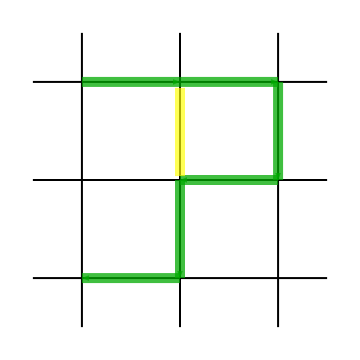

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.004,
hlThc=0.02,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
squareGridFunc[n_,m_]:=(
{
Table[{Black,Thickness[gridThc],Line[{{xi*xStep,-offset*yStep},{xi*xStep,(offset+m-1)*yStep}}]},
{xi,0,n-1}],
Table[{Black,Thickness[gridThc],Line[{{-offset*xStep,yi*yStep},{(offset+n-1)*xStep,yi*yStep}}]},
{yi,0,m-1}]
}//Flatten
);

hlFunc[s_,e_,col_]:=(
{col,Thickness[hlThc],Arrowheads[0.1],Arrow[{s*{xStep,yStep},e*{xStep,yStep}}]}
);

hlFunc2[s_,e_,col_]:=(
{col,Thickness[hlThc],Line[{s*{xStep,yStep},e*{xStep,yStep}}]}
);

hlPathFunc[pathNodes_,col_]:=(
Table[
hlFunc[pathNodes[[it]],pathNodes[[it+1]],col],
{it,Length[pathNodes]-1}]//Flatten
);

paths03=Show[Graphics[
{
squareGridFunc[3,3],
hlPathFunc[{{1,2},{2,2},{3,2},{3,1},{2,1},{2,0},{1,0}}-Table[{1,0},7],Opacity[0.75,Darker[Green]]],
hlFunc2[{1,1.94},{1,1.04},Opacity[0.67,Yellow]]
},
Epilog->{Inset[MaTeX["\\mathrm{(b)}",Magnification->4],Scaled[{-0.02,0.83}],{0,0}]}
],ImageSize->Medium]
)];
paths03
```

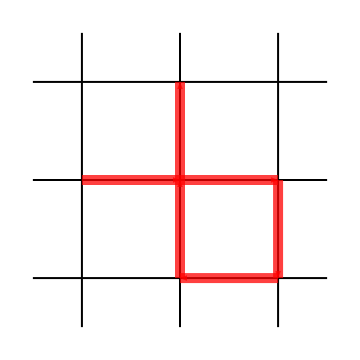

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.004,
hlThc=0.02,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
squareGridFunc[n_,m_]:=(
{
Table[{Black,Thickness[gridThc],Line[{{xi*xStep,-offset*yStep},{xi*xStep,(offset+m-1)*yStep}}]},
{xi,0,n-1}],
Table[{Black,Thickness[gridThc],Line[{{-offset*xStep,yi*yStep},{(offset+n-1)*xStep,yi*yStep}}]},
{yi,0,m-1}]
}//Flatten
);

hlFunc[s_,e_,col_]:=(
{col,Thickness[hlThc],Arrowheads[0.1],Arrow[{s*{xStep,yStep},e*{xStep,yStep}}]}
);

hlPathFunc[pathNodes_,col_]:=(
Table[
hlFunc[pathNodes[[it]],pathNodes[[it+1]],col],
{it,Length[pathNodes]-1}]//Flatten
);

paths04=Show[Graphics[
{
squareGridFunc[3,3],
hlPathFunc[{{1,2},{2,2},{3,2},{3,1},{2,1},{2,2},{2,3}}-Table[{1,1},7],Opacity[0.75,Red]]
},
Epilog->{Inset[MaTeX["\\mathrm{(d)}",Magnification->4],Scaled[{-0.02,0.83}],{0,0}]}
],ImageSize->Medium]
)];
paths04
```

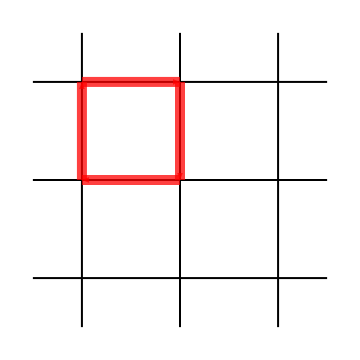

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.004,
hlThc=0.02,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
squareGridFunc[n_,m_]:=(
{
Table[{Black,Thickness[gridThc],Line[{{xi*xStep,-offset*yStep},{xi*xStep,(offset+m-1)*yStep}}]},
{xi,0,n-1}],
Table[{Black,Thickness[gridThc],Line[{{-offset*xStep,yi*yStep},{(offset+n-1)*xStep,yi*yStep}}]},
{yi,0,m-1}]
}//Flatten
);

hlFunc[s_,e_,col_]:=(
{col,Thickness[hlThc],Arrowheads[0.1],Arrow[{s*{xStep,yStep},e*{xStep,yStep}}]}
);

hlPathFunc[pathNodes_,col_]:=(
Table[
hlFunc[pathNodes[[it]],pathNodes[[it+1]],col],
{it,Length[pathNodes]-1}]//Flatten
);

paths02=Show[Graphics[
{
squareGridFunc[3,3],
hlPathFunc[{{2,2},{3,2},{3,1},{2,1},{2,2}}-Table[{2,0},5],Opacity[0.75,Red]]
},
Epilog->{Inset[MaTeX["\\mathrm{(c)}",Magnification->4],Scaled[{-0.02,0.83}],{0,0}]}
],ImageSize->Medium]
)];
paths02
```

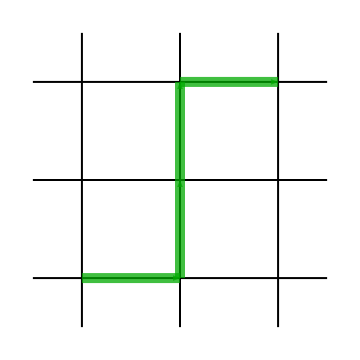

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.004,
hlThc=0.02,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
squareGridFunc[n_,m_]:=(
{
Table[{Black,Thickness[gridThc],Line[{{xi*xStep,-offset*yStep},{xi*xStep,(offset+m-1)*yStep}}]},
{xi,0,n-1}],
Table[{Black,Thickness[gridThc],Line[{{-offset*xStep,yi*yStep},{(offset+n-1)*xStep,yi*yStep}}]},
{yi,0,m-1}]
}//Flatten
);

hlFunc[s_,e_,col_]:=(
{col,Thickness[hlThc],Arrowheads[0.1],Arrow[{s*{xStep,yStep},e*{xStep,yStep}}]}
);

hlPathFunc[pathNodes_,col_]:=(
Table[
hlFunc[pathNodes[[it]],pathNodes[[it+1]],col],
{it,Length[pathNodes]-1}]//Flatten
);

paths01=Show[Graphics[
{
squareGridFunc[3,3],
hlPathFunc[{{0,0},{1,0},{1,1},{1,2},{2,2}},Opacity[0.75,Darker[Green]]]
},
Epilog->{Inset[MaTeX["\\mathrm{(a)}",Magnification->4],Scaled[{-0.02,0.83}],{0,0}]}
],ImageSize->Medium]
)];
paths01
```

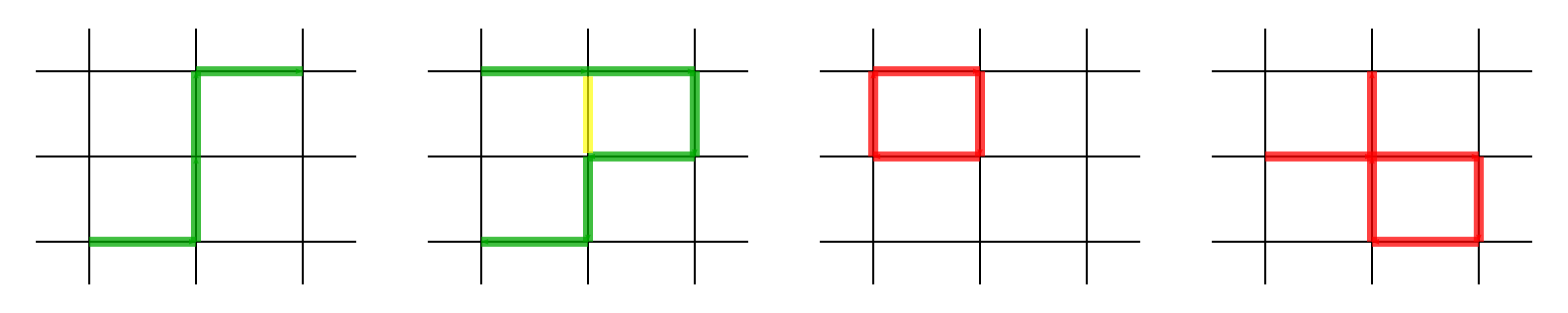

```mathematica
fig=Grid[{{paths01,paths03,paths02,paths04}}]
```

```mathematica
Export["paths.png",fig,ImageResolution->300]
```

paths.png

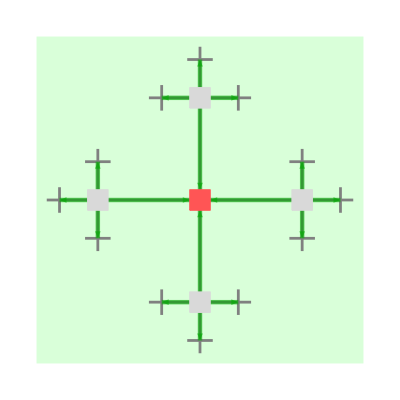

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.005,
hlThc=0.008,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
betheGridFunc[]:=(
{
Gray,Thickness[gridThc],
Line[{{-1.5,0},{1.5,0}}],
Line[{{0,-1.5},{0,1.5}}],
Line[{{1,-0.5},{1,0.5}}],
Line[{{-1,-0.5},{-1,0.5}}],
Line[{{-0.5,1},{0.5,1}}],
Line[{{-0.5,-1},{0.5,-1}}],

Line[{{1.375,-0.125},{1.375,0.125}}],
Line[{{-1.375,-0.125},{-1.375,0.125}}],
Line[{{-0.125,1.375},{0.125,1.375}}],
Line[{{-0.125,-1.375},{0.125,-1.375}}],
Line[{{1-0.125,-0.375},{1+0.125,-0.375}}],
Line[{{1-0.125,0.375},{1+0.125,0.375}}],
Line[{{0.125-1,-0.375},{-1-0.125,-0.375}}],
Line[{{0.125-1,0.375},{-1-0.125,0.375}}],

Line[{{-0.375,1-0.125},{-0.375,1+0.125}}],
Line[{{0.375,1-0.125},{0.375,1+0.125}}],
Line[{{-0.375,0.125-1},{-0.375,-1-0.125}}],
Line[{{0.375,0.125-1},{0.375,-1-0.125}}]
}//Flatten
);

bgFun[{xc_,yc_},{w_,h_},col_]:={col,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

hlFunc[s_,e_,col_,ah_:0.06]:=(
{col,Thickness[hlThc],Arrowheads[ah],Arrow[{s,e}]}
);

magnon[{xc_,yc_},{w_,h_}]:={EdgeForm[Thick],Lighter[Red],Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]/2]};
hole[{xc_,yc_},{w_,h_},edge_]:={EdgeForm[Directive[Thick,edge]],LightGray,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

paths1=Graphics[
{
bgFun[{0,0},{1.6,1.6},Opacity[0.15,Green]],
betheGridFunc[],

hlFunc[{0,0.9},{0,0.1},Opacity[0.6, Darker[Green]]],
hlFunc[{0.9,0},{0.1,0},Opacity[0.6, Darker[Green]]],
hlFunc[{0,-0.9},{0,-0.1},Opacity[0.6, Darker[Green]]],
hlFunc[{-0.9,0},{-0.1,0},Opacity[0.6, Darker[Green]]],

hlFunc[{0,1},{0,1.375},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{0,1},{0.375,1},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{0,1},{-0.375,1},Opacity[0.6, Darker[Green]],0.045],

hlFunc[{0,-1},{0,-1.375},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{0,-1},{0.375,-1},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{0,-1},{-0.375,-1},Opacity[0.6, Darker[Green]],0.045],

hlFunc[{1,0},{1.375,0},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{1,0},{1,0.375},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{1,0},{1,-0.375},Opacity[0.6, Darker[Green]],0.045],

hlFunc[{-1,0},{-1.375,0},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{-1,0},{-1,0.375},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{-1,0},{-1,-0.375},Opacity[0.6, Darker[Green]],0.045],

magnon[{0,0},{0.1,0.1}],
hole[{1,0},{0.1,0.1},Dashed],
hole[{0,1},{0.1,0.1},Dashed],
hole[{-1,0},{0.1,0.1},Dashed],
hole[{0,-1},{0.1,0.1},Dashed],

Inset[MaTeX["\\varphi_0 = 0",Magnification->2],Scaled[{0.7,0.56}]],
Inset[MaTeX["\\varphi_1 = 0",Magnification->2],Scaled[{0.63,0.89}]],
Inset[MaTeX["\\varphi_2 = 0",Magnification->2],Scaled[{0.31,0.46}]],
Inset[MaTeX["\\varphi_3 = 0",Magnification->2],Scaled[{0.63,0.27}]]
},
Frame->False,
PlotRange->{{-1.6,1.6},{-1.6,1.6}},
PlotRangeClipping->True
]
)];
paths1
```

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.005,
hlThc=0.008,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
betheGridFunc[]:=(
{
Gray,Thickness[gridThc],
Line[{{-1.5,0},{1.5,0}}],
Line[{{0,-1.5},{0,1.5}}],
Line[{{1,-0.5},{1,0.5}}],
Line[{{-1,-0.5},{-1,0.5}}],
Line[{{-0.5,1},{0.5,1}}],
Line[{{-0.5,-1},{0.5,-1}}],

Line[{{1.375,-0.125},{1.375,0.125}}],
Line[{{-1.375,-0.125},{-1.375,0.125}}],
Line[{{-0.125,1.375},{0.125,1.375}}],
Line[{{-0.125,-1.375},{0.125,-1.375}}],
Line[{{1-0.125,-0.375},{1+0.125,-0.375}}],
Line[{{1-0.125,0.375},{1+0.125,0.375}}],
Line[{{0.125-1,-0.375},{-1-0.125,-0.375}}],
Line[{{0.125-1,0.375},{-1-0.125,0.375}}],

Line[{{-0.375,1-0.125},{-0.375,1+0.125}}],
Line[{{0.375,1-0.125},{0.375,1+0.125}}],
Line[{{-0.375,0.125-1},{-0.375,-1-0.125}}],
Line[{{0.375,0.125-1},{0.375,-1-0.125}}]
}//Flatten
);

hlFunc[s_,e_,col_,ah_:0.06]:=(
{col,Thickness[hlThc],Arrowheads[ah],Arrow[{s,e}]}
);

bgFun[{xc_,yc_},{w_,h_},col_]:={col,Rotate[Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]/2],45Degree]};

magnon[{xc_,yc_},{w_,h_}]:={EdgeForm[Thick],Lighter[Red],Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]/2]};
hole[{xc_,yc_},{w_,h_},edge_]:={EdgeForm[Directive[Thick,edge]],LightGray,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

paths2=Graphics[
{
bgFun[{2.,0},{1.25,1.25},Opacity[0.15,Green]],
bgFun[{-2.,0},{1.25,1.25},Opacity[0.15,Green]],
bgFun[{0,2.},{1.25,1.25},Opacity[0.15,Green]],
bgFun[{0,-2.},{1.25,1.25},Opacity[0.15,Green]],

betheGridFunc[],

hlFunc[{0,0.9},{0,0.1},Opacity[0.6, Red]],
hlFunc[{0.9,0},{0.1,0},Opacity[0.6, Red]],
hlFunc[{0,-0.9},{0,-0.1},Opacity[0.6, Red]],
hlFunc[{-0.9,0},{-0.1,0},Opacity[0.6, Red]],

hlFunc[{0,1},{0,1.375},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{0,1},{0.375,1},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{0,1},{-0.375,1},Opacity[0.6, Darker[Green]],0.045],

hlFunc[{0,-1},{0,-1.375},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{0,-1},{0.375,-1},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{0,-1},{-0.375,-1},Opacity[0.6, Darker[Green]],0.045],

hlFunc[{1,0},{1.375,0},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{1,0},{1,0.375},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{1,0},{1,-0.375},Opacity[0.6, Darker[Green]],0.045],

hlFunc[{-1,0},{-1.375,0},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{-1,0},{-1,0.375},Opacity[0.6, Darker[Green]],0.045],
hlFunc[{-1,0},{-1,-0.375},Opacity[0.6, Darker[Green]],0.045],

magnon[{0,0},{0.1,0.1}],
hole[{1,0},{0.1,0.1},Dashed],
hole[{0,1},{0.1,0.1},Dashed],
hole[{-1,0},{0.1,0.1},Dashed],
hole[{0,-1},{0.1,0.1},Dashed],
Inset[MaTeX["\\varphi_0 = 0",Magnification->2],Scaled[{0.7,0.56}]],
Inset[MaTeX["\\varphi_1 = \\frac{\\pi}{2}",Magnification->2],Scaled[{0.63,0.89}]],
Inset[MaTeX["\\varphi_2 = \\pi",Magnification->2],Scaled[{0.31,0.46}]],
Inset[MaTeX["\\varphi_3 = \\frac{3\\pi}{2}",Magnification->2],Scaled[{0.645,0.27}]]
},
Frame->False,
PlotRange->{{-1.6,1.6},{-1.6,1.6}},
PlotRangeClipping->True
]
)];
paths2
```

-Graphics-

```mathematica
names={
Export["cart2_a.png",paths1,ImageResolution->300],
Export["cart2_b.png",paths2,ImageResolution->300]
}
```

{cart2_a.png,cart2_b.png}

```mathematica
figs=Table[Import[name],{name,names}]
```

{-Graphics-,-Graphics-}

```mathematica
labels={MaTeX["\\mathrm{(a)}",Magnification->2.25],MaTeX["\\mathrm{(b)}",Magnification->2.25]};
```

```mathematica
figsLabeled=Table[Show[figs[[it]],ImageSize->Medium,Epilog->{Inset[labels[[it]],Scaled[{0.05,0.95}]]}],{it,2}]
```

{-Graphics-,-Graphics-}

```mathematica
figsGrid=Grid[{figsLabeled},Spacings->{2, 1}]
```

-Graphics- | -Graphics-

```mathematica
Export["cartoon2.png",figsGrid,ImageResolution->300]
```

cartoon2.png

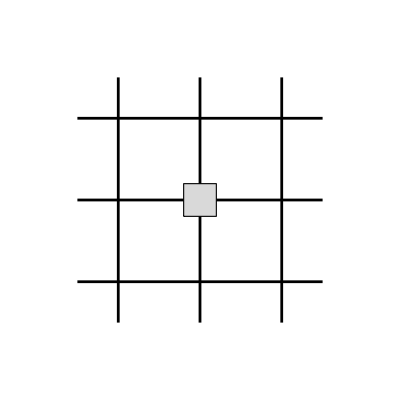

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.005,
hlThc=0.008,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
squareGridFunc[n_,m_]:=(
{
Table[{Black,Thickness[gridThc],Line[{{xi*xStep,-offset*yStep},{xi*xStep,(offset+m-1)*yStep}}]},
{xi,0,n-1}],
Table[{Black,Thickness[gridThc],Line[{{-offset*xStep,yi*yStep},{(offset+n-1)*xStep,yi*yStep}}]},
{yi,0,m-1}]
}//Flatten
);

bgFun[{xc_,yc_},{w_,h_},col_]:={col,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

hlFunc[s_,e_,col_,ah_:0.06]:=(
{col,Thickness[hlThc],Arrowheads[ah],Arrow[{s,e}]}
);

magnon[{xc_,yc_},{w_,h_}]:={EdgeForm[Thick],Lighter[Red],Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]/2]};
hole[{xc_,yc_},{w_,h_},edge_]:={EdgeForm[Directive[Thick,edge]],LightGray,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

paths30=Graphics[
{
squareGridFunc[3,3],

(*hlFunc[{0.1,0},{0.9,0},Opacity[0.6,Lighter[Blue]]],
hlFunc[{1,0},{1,-0.9},Opacity[0.6,Lighter[Blue]],0.055],
hlFunc[{1,-1},{0.1,-1},Opacity[0.6,Lighter[Blue]],0.05],

hlFunc[{0,-1},{0,-0.1},Opacity[0.6,Red],0.045],
hlFunc[{0,-1},{0,-1.5},Opacity[0.6,Darker[Green]],0.045],
hlFunc[{0,-1},{-0.5,-1},Opacity[0.6,Darker[Green]],0.045],*)

hole[{1,1},{0.2,0.2},Black],

Inset[MaTeX["\\mathrm{(a)}~l=0",Magnification->2.5],Scaled[{0.05,0.88}],{0,0}]

},
Frame->False,
PlotRange->{{-1,3},{-1,3}},
PlotRangeClipping->True,
Prolog->{Inset[Graphics[{Opacity[0.2,Gray],Rectangle[{-1.5,-1.5},{1.5,1.5},RoundingRadius->.3]}],{1,1},{0,0},3.25]}
]
)];
paths30
```

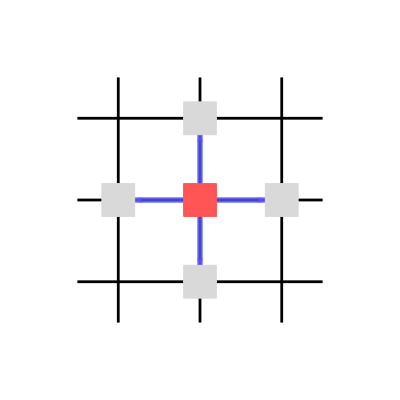

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.005,
hlThc=0.01,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
squareGridFunc[n_,m_]:=(
{
Table[{Black,Thickness[gridThc],Line[{{xi*xStep,-offset*yStep},{xi*xStep,(offset+m-1)*yStep}}]},
{xi,0,n-1}],
Table[{Black,Thickness[gridThc],Line[{{-offset*xStep,yi*yStep},{(offset+n-1)*xStep,yi*yStep}}]},
{yi,0,m-1}]
}//Flatten
);

bgFun[{xc_,yc_},{w_,h_},col_]:={col,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

hlFunc[s_,e_,col_,ah_:0.07]:=(
{col,Thickness[hlThc],Arrowheads[ah],Arrow[{s,e}]}
);

magnon[{xc_,yc_},{w_,h_}]:={EdgeForm[Thick],Lighter[Red],Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]/2]};
hole[{xc_,yc_},{w_,h_},edge_]:={EdgeForm[Directive[Thick,edge]],LightGray,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

paths31=Graphics[
{
squareGridFunc[3,3],

hlFunc[{1.2,1},{1.8,1},Opacity[0.8,Lighter[Blue]]],
hlFunc[{0.8,1},{0.2,1},Opacity[0.8,Lighter[Blue]]],
hlFunc[{1,1.2},{1,1.8},Opacity[0.8,Lighter[Blue]]],
hlFunc[{1,0.8},{1,0.2},Opacity[0.8,Lighter[Blue]]],

hole[{2,1},{0.2,0.2},Dashed],
hole[{1,2},{0.2,0.2},Dashed],
hole[{0,1},{0.2,0.2},Dashed],
hole[{1,0},{0.2,0.2},Dashed],

magnon[{1,1},{0.2,0.2}],

Inset[MaTeX["\\mathrm{(b)}~l=1",Magnification->2.5],Scaled[{0.05,0.88}],{0,0}],
Inset[MaTeX["1",Magnification->2.5],Scaled[{0.77,0.52}],{0,0}],
Inset[MaTeX["\\textit{e}^{\\frac{i\\pi}{2}m_4^{(1)}}",Magnification->2.5],Scaled[{0.52,0.77}],{0,0}],
Inset[MaTeX["\\textit{e}^{i\\pi m_4^{(1)}}",Magnification->2.5],Scaled[{0.02,0.52}],{0,0}],
Inset[MaTeX["\\textit{e}^{\\frac{3i\\pi}{2}m_4^{(1)}}",Magnification->2.5],Scaled[{0.495,0.09}],{0,0}]

},
Frame->False,
PlotRange->{{-1,3},{-1,3}},
PlotRangeClipping->True,
Prolog->{Inset[Graphics[{Opacity[0.25,Yellow],Disk[{0.75,-0.5},{1,0.4}]}],Scaled[{0.63,0.5}]]}
]
)];
paths31
```

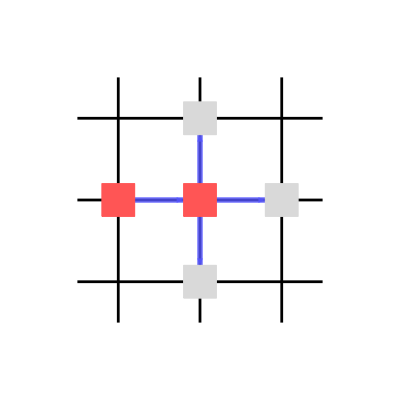

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.005,
hlThc=0.01,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
squareGridFunc[n_,m_]:=(
{
Table[{Black,Thickness[gridThc],Line[{{xi*xStep,-offset*yStep},{xi*xStep,(offset+m-1)*yStep}}]},
{xi,0,n-1}],
Table[{Black,Thickness[gridThc],Line[{{-offset*xStep,yi*yStep},{(offset+n-1)*xStep,yi*yStep}}]},
{yi,0,m-1}]
}//Flatten
);

bgFun[{xc_,yc_},{w_,h_},col_]:={col,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

hlFunc[s_,e_,col_,ah_:0.07]:=(
{col,Thickness[hlThc],Arrowheads[ah],Arrow[{s,e}]}
);

magnon[{xc_,yc_},{w_,h_}]:={EdgeForm[Thick],Lighter[Red],Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]/2]};
hole[{xc_,yc_},{w_,h_},edge_]:={EdgeForm[Directive[Thick,edge]],LightGray,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

paths32=Graphics[
{
squareGridFunc[3,3],

hlFunc[{1.2,1},{1.8,1},Opacity[0.8,Lighter[Blue]]],
hlFunc[{0.2,1},{0.8,1},Opacity[0.8,Lighter[Blue]]],
hlFunc[{1,1.2},{1,1.8},Opacity[0.8,Lighter[Blue]]],
hlFunc[{1,0.8},{1,0.2},Opacity[0.8,Lighter[Blue]]],

hole[{2,1},{0.2,0.2},Dashed],
hole[{1,2},{0.2,0.2},Dashed],
hole[{1,0},{0.2,0.2},Dashed],

magnon[{0,1},{0.2,0.2}],
magnon[{1,1},{0.2,0.2}],

Inset[MaTeX["\\mathrm{(c)}~n=2",Magnification->2.5],Scaled[{0.05,0.88}],{0,0}],

Inset[MaTeX["1",Magnification->2.5],Scaled[{0.77,0.52}],{0,0}],
Inset[MaTeX["\\textit{e}^{\\frac{2\\pi i}{3}m_3^{(2)}}",Magnification->2.5],Scaled[{0.495,0.78}],{0,0}],
Inset[MaTeX["\\textit{e}^{\\frac{4\\pi i}{3}m_3^{(2)}}",Magnification->2.5],Scaled[{0.495,0.09}],{0,0}],

Inset[MaTeX["\\mathrm{x4~rotations}",Magnification->2],Scaled[{0.7,0.06}]]

},
Frame->False,
PlotRange->{{-1,3},{-1,3}},
PlotRangeClipping->True,
Prolog->{Inset[Graphics[{Opacity[0.25,Yellow],Disk[{0.75,-0.5},{1,0.4}]}],Scaled[{0.63-0.25,0.5}]]}
]
)];
paths32
```

```mathematica
plist={paths30,paths31,paths32};
```

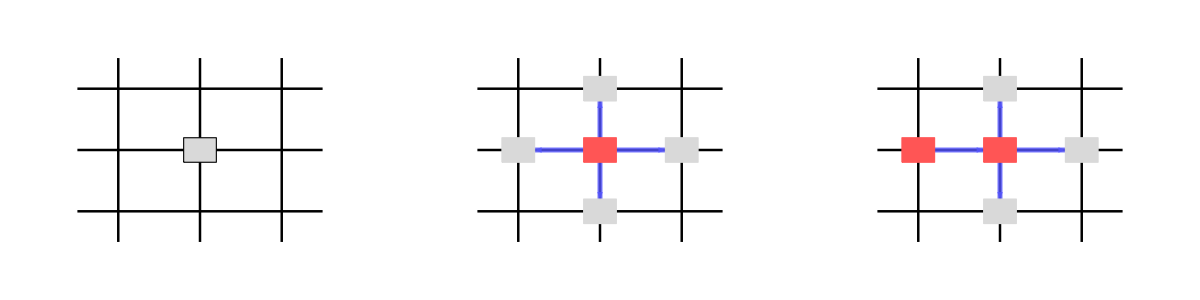

```mathematica
rotCart=Grid[{Table[Show[p,ImageSize->Medium],{p,plist}]},Spacings->{-2,0}]
```

```mathematica
Export["rot_cartoon.png",rotCart,ImageResolution->300]
```

rot_cartoon.png

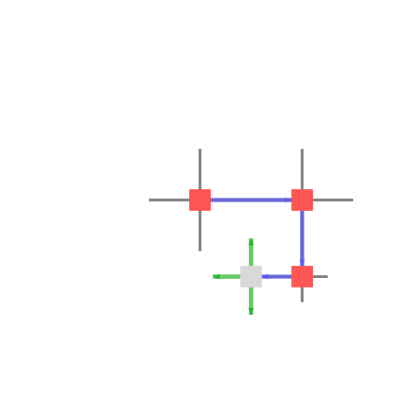

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.005,
hlThc=0.008,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
betheGridFunc[]:=(
{
Gray,Thickness[gridThc],
Line[{{-0.5,0},{1.5,0}}],
Line[{{0,-0.5},{0,0.5}}],
Line[{{1,-1},{1,0.5}}],
Line[{{0.5,-0.75},{1.25,-0.75}}]

(*Line[{{0.5,-1.125},{0.5,-0.375}}]
Line[{{0.375,-0.5},{0.625,-0.5}}],
Line[{{0.375,-1},{0.625,-1}}],
Line[{{0.25,-0.875},{0.25,-0.625}}]*)


}//Flatten
);

bgFun[{xc_,yc_},{w_,h_},col_]:={col,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

hlFunc[s_,e_,col_,ah_:0.06]:=(
{col,Thickness[hlThc],Arrowheads[ah],Arrow[{s,e}]}
);

magnon[{xc_,yc_},{w_,h_}]:={EdgeForm[Thick],Lighter[Red],Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]/2]};
hole[{xc_,yc_},{w_,h_},edge_]:={EdgeForm[Directive[Thick,edge]],LightGray,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

paths4=Graphics[
{
betheGridFunc[],

hlFunc[{0.1,0},{0.9,0},Opacity[0.6,Lighter[Blue]]],
hlFunc[{1,-0.1},{1,-0.65},Opacity[0.6,Lighter[Blue]],0.055],
hlFunc[{0.9,-0.75},{0.6,-0.75},Opacity[0.6,Lighter[Blue]],0.05],

hlFunc[{0.5,-0.75},{0.5,-0.375},Opacity[0.6,Darker[Green]],0.045],
hlFunc[{0.5,-0.75},{0.5,-1.125},Opacity[0.6,Darker[Green]],0.045],
hlFunc[{0.5,-0.75},{0.125,-0.75},Opacity[0.6,Darker[Green]],0.045],

magnon[{0,0},{0.1,0.1}],
magnon[{1,0},{0.1,0.1}],
magnon[{1,-0.75},{0.1,0.1}],
hole[{0.5,-0.75},{0.1,0.1},Dashed],

Inset[MaTeX["\\mathrm{(b)}~H",Magnification->2],Scaled[{0.24,0.85}]]

},
Frame->False,
PlotRange->{{-1.6,1.6},{-1.6,1.6}},
PlotRangeClipping->True
]
)];
paths4
```

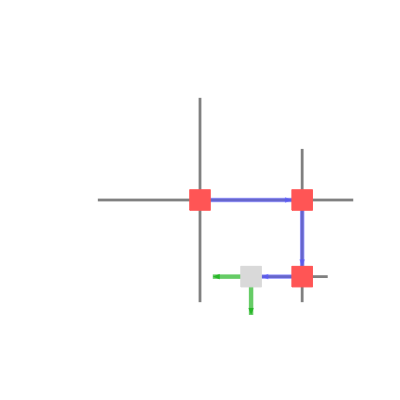

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.005,
hlThc=0.008,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
betheGridFunc[]:=(
{
Gray,Thickness[gridThc],
Line[{{-1,0},{1.5,0}}],
Line[{{0,-1},{0,1}}],
Line[{{1,-1},{1,0.5}}],
Line[{{0.5,-0.75},{1.25,-0.75}}]

(*Line[{{0.5,-1.125},{0.5,-0.375}}]
Line[{{0.375,-0.5},{0.625,-0.5}}],
Line[{{0.375,-1},{0.625,-1}}],
Line[{{0.25,-0.875},{0.25,-0.625}}]*)


}//Flatten
);

bgFun[{xc_,yc_},{w_,h_},col_]:={col,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

hlFunc[s_,e_,col_,ah_:0.06]:=(
{col,Thickness[hlThc],Arrowheads[ah],Arrow[{s,e}]}
);

magnon[{xc_,yc_},{w_,h_}]:={EdgeForm[Thick],Lighter[Red],Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]/2]};
hole[{xc_,yc_},{w_,h_},edge_]:={EdgeForm[Directive[Thick,edge]],LightGray,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

paths5=Graphics[
{
betheGridFunc[],

hlFunc[{0.1,0},{0.9,0},Opacity[0.6,Lighter[Blue]]],
hlFunc[{1,-0.1},{1,-0.65},Opacity[0.6,Lighter[Blue]],0.055],
hlFunc[{0.9,-0.75},{0.6,-0.75},Opacity[0.6,Lighter[Blue]],0.05],

hlFunc[{0.5,-0.75},{0.5,-1.125},Opacity[0.6,Darker[Green]],0.045],
hlFunc[{0.5,-0.75},{0.125,-0.75},Opacity[0.6,Darker[Green]],0.045],

magnon[{0,0},{0.1,0.1}],
magnon[{1,0},{0.1,0.1}],
magnon[{1,-0.75},{0.1,0.1}],
hole[{0.5,-0.75},{0.1,0.1},Dashed],

Inset[MaTeX["\\mathrm{(c)}~H + H'",Magnification->2],Scaled[{0.3,0.85}]]

},
Frame->False,
PlotRange->{{-1.6,1.6},{-1.6,1.6}},
PlotRangeClipping->True
]
)];
paths5
```

```mathematica
ps={paths3,paths4,paths5};
```

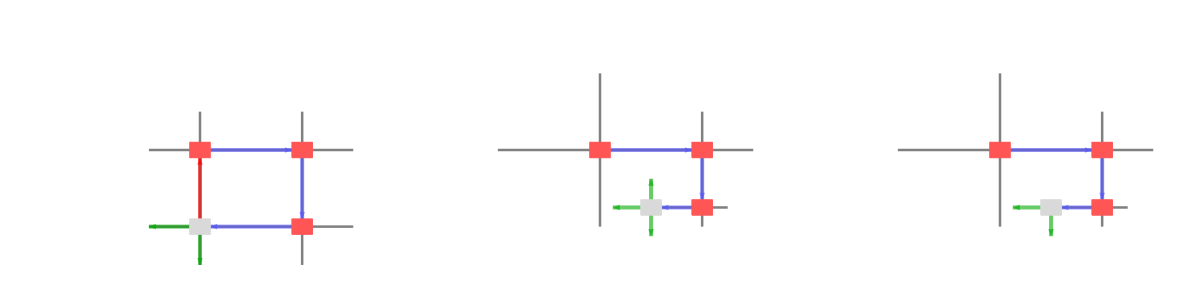

```mathematica
fig=Grid[{Table[Show[p,ImageSize->Medium],{p,ps}]}]
```

```mathematica
Export["cartoon1grid.png",fig,ImageResolution->300]
```

cartoon1grid.png

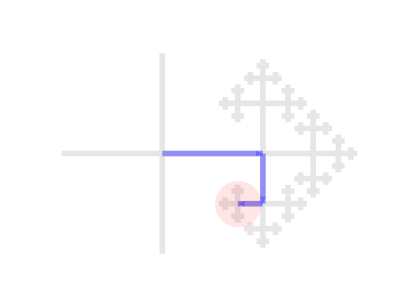

```mathematica
Module[
{
holeFillingColor=Lighter[Blue],(*Darker[Blend[{Blue,Darker[Cyan]},0.5]];*)
magnonFillingColor=Lighter[Red],
eraserColor=White,
h=0.55,
hw=0.2,
r=0.1,
lineThickness=0.01
},(
GetLattice[depths_:{6,1},scaling_:1]:=Module[
{vertices,coordinates,edges,parent,vertex,index,angle,SpanLattice},(

SpanLattice[d_,depth_,lastAngle_,s_,localParent_]:=Module[{localVertex,localAngle,it},(
If[d<depth,(
For[it=1,it<Length[depths],it++,(
localVertex=vertices[[-1]]+1;
localAngle=2Pi it/Length[depths];
AppendTo[vertices,localVertex];
AppendTo[coordinates,coordinates[[localParent]]+
s*{Cos[lastAngle-Pi+localAngle],Sin[lastAngle-Pi+localAngle]}];
AppendTo[edges,localParent<->localVertex];
SpanLattice[d+1,depth,lastAngle-Pi+localAngle,s*scaling,localVertex];
)]
)]
)];

vertices={1};
coordinates={{0,0}};
edges={};
index=0;
parent=vertices[[1]];
Do[(
vertex=vertices[[-1]]+1;
angle=2Pi index/Length[depths];
AppendTo[vertices,vertex];
AppendTo[coordinates,coordinates[[parent]]+1{Cos[angle],Sin[angle]}];
AppendTo[edges,parent<->vertex];
SpanLattice[1,depth,angle,scaling,vertex];
index+=1;
),
{depth,depths}];
{vertices,coordinates,edges})];

{v,c,e}=GetLattice[{5,0,0,0},1/Sqrt[4]];
g=Graph[v,e,VertexCoordinates->c,VertexShapeFunction->None,EdgeStyle->Thick,VertexSize->0,VertexLabels->"Name"];

a[x_,y_,h_,color_:Black]:={Thickness[0.0075],color,Arrowheads[0.06],Arrow[{{x,y-h/2},{x,y+h/2}}]};
d[x_,y_,r_,color_,ef_:{Thickness[0.01],Black}]:={EdgeForm[ef],color,Disk[{x,y},r]};
rc[x_,y_,r_,color_,ef_:{Black}]:={EdgeForm[ef],Lighter[color],Disk[{x,y},r]};
er[x_,y_,dx_,dy_,ef_:{White}]:={EdgeForm[ef],eraserColor,Rectangle[{x-dx/2,y-dy/2},{x+dx/2,y+dy/2}]};

bethe[holePath_,step_]:=(
spins={1};
Do[(
AppendTo[spins,-spins[[e[[it-1,1]]]]]
),{it,Complement[v,{1}]}];

hlEdge={};
Do[(
Do[(
If[edge[[1]]==it,
AppendTo[hlEdge,
Line[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{it,holePath[[1;;(step-1)]]}]
),{edge,e}];

hlPath={};
Do[(
Do[(
If[edge==holePath[[it]]<->holePath[[it+1]]||edge==holePath[[it+1]]<->holePath[[it]],
AppendTo[hlPath,
Arrow[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{it,Length[holePath[[1;;step]]]-1}]
),{edge,e}];

hlJumps={};
Do[(
If[edge[[1]]==holePath[[step]],
AppendTo[hlJumps,
Line[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{edge,e}];

hole={d[c[[holePath[[step]],1]],c[[holePath[[step]],2]],r,holeFillingColor]};

oldHole={d[c[[holePath[[1]],1]],c[[holePath[[1]],2]],r,White,{Thickness[0.01],Black,Dashed}]};

baseline=Table[Line[{{c[[e[[n-1,1]],1]],c[[e[[n-1,1]],2]]},{c[[n,1]],c[[n,2]]}}],{n,2,v[[-1]]}];

hlEdge=Complement[hlEdge,hlPath];
(*baseline=Complement[baseline,hlJumps];*)
baseline=Complement[baseline,hlPath];

Join[
{{Opacity[1,LightGray//Lighter],Thickness[lineThickness],baseline}},
(*{{Opacity[0.6,Darker[Green]],Thickness[lineThickness],hlJumps}},*)
{{Opacity[0.6,Blue//Lighter],Thickness[lineThickness],hlPath}}
]
);

g1=Graphics[{bethe[{1,2,3,4},4],Opacity[0.1,Red],Disk[{0.75,-0.5},0.23]},Frame->False,PlotRange->{{-1.25,2},{-1.25,1.25}},PlotRangeClipping->True]
)];
g1
```

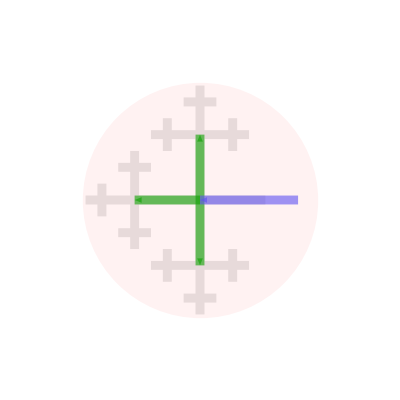

```mathematica
Module[
{
holeFillingColor=Lighter[Blue],(*Darker[Blend[{Blue,Darker[Cyan]},0.5]];*)
magnonFillingColor=Lighter[Red],
eraserColor=White,
h=0.55,
hw=0.2,
r=0.1,
lineThickness=0.01*(2/1.25)
},(
GetLattice[depths_:{6,1},scaling_:1]:=Module[
{vertices,coordinates,edges,parent,vertex,index,angle,SpanLattice},(

SpanLattice[d_,depth_,lastAngle_,s_,localParent_]:=Module[{localVertex,localAngle,it},(
If[d<depth,(
For[it=1,it<Length[depths],it++,(
localVertex=vertices[[-1]]+1;
localAngle=2Pi it/Length[depths];
AppendTo[vertices,localVertex];
AppendTo[coordinates,coordinates[[localParent]]+
s*{Cos[lastAngle-Pi+localAngle],Sin[lastAngle-Pi+localAngle]}];
AppendTo[edges,localParent<->localVertex];
SpanLattice[d+1,depth,lastAngle-Pi+localAngle,s*scaling,localVertex];
)]
)]
)];

vertices={1};
coordinates={{0,0}};
edges={};
index=0;
parent=vertices[[1]];
Do[(
vertex=vertices[[-1]]+1;
angle=2Pi index/Length[depths];
AppendTo[vertices,vertex];
AppendTo[coordinates,coordinates[[parent]]+1{Cos[angle],Sin[angle]}];
AppendTo[edges,parent<->vertex];
SpanLattice[1,depth,angle,scaling,vertex];
index+=1;
),
{depth,depths}];
{vertices,coordinates,edges})];

{v,c,e}=GetLattice[{1,3,3,3},1/Sqrt[4]];
g=Graph[v,e,VertexCoordinates->c,VertexShapeFunction->None,EdgeStyle->Thick,VertexSize->0,VertexLabels->"Name"];

a[x_,y_,h_,color_:Black]:={Thickness[0.0075],color,Arrowheads[0.06],Arrow[{{x,y-h/2},{x,y+h/2}}]};
d[x_,y_,r_,color_,ef_:{Thickness[0.01],Black}]:={EdgeForm[ef],color,Disk[{x,y},r]};
rc[x_,y_,r_,color_,ef_:{Black}]:={EdgeForm[ef],Lighter[color],Disk[{x,y},r]};
er[x_,y_,dx_,dy_,ef_:{White}]:={EdgeForm[ef],eraserColor,Rectangle[{x-dx/2,y-dy/2},{x+dx/2,y+dy/2}]};

bethe[holePath_,step_]:=(
spins={1};
Do[(
AppendTo[spins,-spins[[e[[it-1,1]]]]]
),{it,Complement[v,{1}]}];

hlEdge={};
Do[(
Do[(
If[edge[[1]]==it,
AppendTo[hlEdge,
Line[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{it,holePath[[1;;(step-1)]]}]
),{edge,e}];

hlPath={Arrowheads[0.1]};
Do[(
Do[(
If[edge==holePath[[it]]<->holePath[[it+1]]||edge==holePath[[it+1]]<->holePath[[it]],
AppendTo[hlPath,
Arrow[{{c[[edge[[2]],1]]*1.5,c[[edge[[2]],2]]},{c[[edge[[1]],1]],c[[edge[[1]],2]]}}]
]
]
),{it,Length[holePath[[1;;step]]]-1}]
),{edge,e}];

hlJumps={Arrowheads[0.1]};
Do[(
If[edge[[1]]==holePath[[1]]&&edge[[2]]!=holePath[[step]],
AppendTo[hlJumps,
Arrow[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{edge,e}];

hole={d[c[[holePath[[step]],1]],c[[holePath[[step]],2]],r,holeFillingColor]};

oldHole={d[c[[holePath[[1]],1]],c[[holePath[[1]],2]],r,White,{Thickness[0.01],Black,Dashed}]};

baseline=Table[Line[{{c[[e[[n-1,1]],1]],c[[e[[n-1,1]],2]]},{c[[n,1]],c[[n,2]]}}],{n,2,v[[-1]]}];

hlEdge=Complement[hlEdge,hlPath];
baseline=Complement[baseline,hlJumps];
baseline=Complement[baseline,hlPath];

Join[
{{Opacity[1,LightGray//Lighter],Thickness[lineThickness],baseline}},
{{Opacity[0.6,Darker[Green]],Thickness[lineThickness],hlJumps}},
{{Opacity[0.6,Blue//Lighter],Thickness[lineThickness],hlPath}}
]
);

g2=Graphics[{bethe[{1,2},2],Opacity[0.05,Red],Disk[{0.0,0.0},1.8]},Frame->False,PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotRangeClipping->True]
)];
g2
```

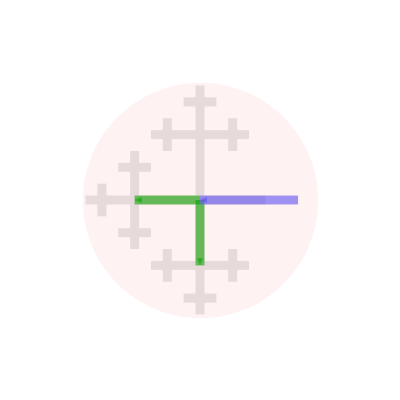

```mathematica
Module[
{
holeFillingColor=Lighter[Blue],(*Darker[Blend[{Blue,Darker[Cyan]},0.5]];*)
magnonFillingColor=Lighter[Red],
eraserColor=White,
h=0.55,
hw=0.2,
r=0.1,
lineThickness=0.01*(2/1.25)
},(
GetLattice[depths_:{6,1},scaling_:1]:=Module[
{vertices,coordinates,edges,parent,vertex,index,angle,SpanLattice},(

SpanLattice[d_,depth_,lastAngle_,s_,localParent_]:=Module[{localVertex,localAngle,it},(
If[d<depth,(
For[it=1,it<Length[depths],it++,(
localVertex=vertices[[-1]]+1;
localAngle=2Pi it/Length[depths];
AppendTo[vertices,localVertex];
AppendTo[coordinates,coordinates[[localParent]]+
s*{Cos[lastAngle-Pi+localAngle],Sin[lastAngle-Pi+localAngle]}];
AppendTo[edges,localParent<->localVertex];
SpanLattice[d+1,depth,lastAngle-Pi+localAngle,s*scaling,localVertex];
)]
)]
)];

vertices={1};
coordinates={{0,0}};
edges={};
index=0;
parent=vertices[[1]];
Do[(
vertex=vertices[[-1]]+1;
angle=2Pi index/Length[depths];
AppendTo[vertices,vertex];
AppendTo[coordinates,coordinates[[parent]]+1{Cos[angle],Sin[angle]}];
AppendTo[edges,parent<->vertex];
SpanLattice[1,depth,angle,scaling,vertex];
index+=1;
),
{depth,depths}];
{vertices,coordinates,edges})];

{v,c,e}=GetLattice[{1,3,3,3},1/Sqrt[4]];
g=Graph[v,e,VertexCoordinates->c,VertexShapeFunction->None,EdgeStyle->Thick,VertexSize->0,VertexLabels->"Name"];

a[x_,y_,h_,color_:Black]:={Thickness[0.0075],color,Arrowheads[0.06],Arrow[{{x,y-h/2},{x,y+h/2}}]};
d[x_,y_,r_,color_,ef_:{Thickness[0.01],Black}]:={EdgeForm[ef],color,Disk[{x,y},r]};
rc[x_,y_,r_,color_,ef_:{Black}]:={EdgeForm[ef],Lighter[color],Disk[{x,y},r]};
er[x_,y_,dx_,dy_,ef_:{White}]:={EdgeForm[ef],eraserColor,Rectangle[{x-dx/2,y-dy/2},{x+dx/2,y+dy/2}]};

bethe[holePath_,step_]:=(
spins={1};
Do[(
AppendTo[spins,-spins[[e[[it-1,1]]]]]
),{it,Complement[v,{1}]}];

hlEdge={};
Do[(
Do[(
If[edge[[1]]==it,
AppendTo[hlEdge,
Line[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{it,holePath[[1;;(step-1)]]}]
),{edge,e}];

hlPath={Arrowheads[0.1]};
Do[(
Do[(
If[edge==holePath[[it]]<->holePath[[it+1]]||edge==holePath[[it+1]]<->holePath[[it]],
AppendTo[hlPath,
Arrow[{{c[[edge[[2]],1]]*1.5,c[[edge[[2]],2]]},{c[[edge[[1]],1]],c[[edge[[1]],2]]}}]
]
]
),{it,Length[holePath[[1;;step]]]-1}]
),{edge,e}];

hlJumps={Arrowheads[0.1]};
Do[(
If[edge[[1]]==holePath[[1]]&&edge[[2]]!=holePath[[step]]&&edge[[2]]!=3,
AppendTo[hlJumps,
Arrow[{{c[[edge[[1]],1]],c[[edge[[1]],2]]},{c[[edge[[2]],1]],c[[edge[[2]],2]]}}]
]
]
),{edge,e}];

hole={d[c[[holePath[[step]],1]],c[[holePath[[step]],2]],r,holeFillingColor]};

oldHole={d[c[[holePath[[1]],1]],c[[holePath[[1]],2]],r,White,{Thickness[0.01],Black,Dashed}]};

baseline=Table[Line[{{c[[e[[n-1,1]],1]],c[[e[[n-1,1]],2]]},{c[[n,1]],c[[n,2]]}}],{n,2,v[[-1]]}];

hlEdge=Complement[hlEdge,hlPath];
baseline=Complement[baseline,hlJumps];
baseline=Complement[baseline,hlPath];

Join[
{{Opacity[1,LightGray//Lighter],Thickness[lineThickness],baseline}},
{{Opacity[0.6,Darker[Green]],Thickness[lineThickness],hlJumps}},
{{Opacity[0.6,Blue//Lighter],Thickness[lineThickness],hlPath}}
]
);

g3=Graphics[{bethe[{1,2},2],Opacity[0.05,Red],Disk[{0.0,0.0},1.8]},Frame->False,PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotRangeClipping->True]
)];
g3
```

```mathematica
griD={Grid[{#},Dividers->{None,None},Alignment->{Left,Center},ItemSize->{Scaled[0.4/Length[#]],2}]}&;
```

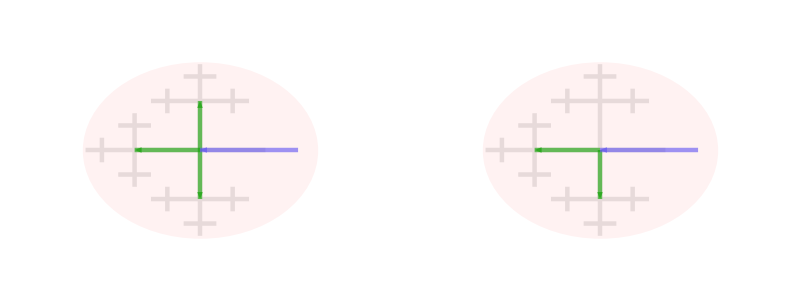
-Graphics-
-Graphics-

```mathematica
plts={
{Show[g1,ImageSize->400,Epilog->{Inset[MaTeX["\\mathrm{(a)}",Magnification->1.5],Scaled[{0, 0.85}],{0,0}]}]},
{
Show[g2,ImageSize->200,Epilog->{Inset[MaTeX["\\mathrm{(b)}~\\hat{H}",Magnification->1.5],Scaled[{0.01, 0.83}],{0,0}]}],
Show[g3,ImageSize->200,Epilog->{Inset[MaTeX["\\mathrm{(c)}~\\hat{H}+\\hat{H}'",Magnification->1.5],Scaled[{0.01, 0.83}],{0,0}]}]
}
};
pt2=Grid[griD/@plts,Frame->None,Spacings->{0,-1}]
```

```mathematica
Export["cartoon1.png",pt2,ImageResolution->300]
```

cartoon1.png

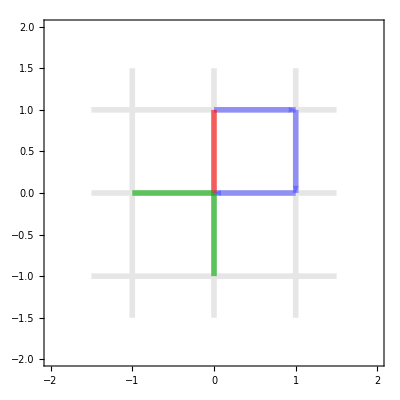

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.01,
hlThc=0.01,
squareGridFunc,
hlFunc,
hlPathFunc
},(

betheGridFunc[]:=(
{
Opacity[1,LightGray//Lighter],Thickness[gridThc],
Line[{{-1.5,0},{1.5,0}}],
Line[{{-1.5,1},{1.5,1}}],
Line[{{-1.5,-1},{1.5,-1}}],

Line[{{0,-1.5},{0,1.5}}],
Line[{{1,-1.5},{1,1.5}}],
Line[{{-1,-1.5},{-1,1.5}}]



}//Flatten
);

hlFunc[s_,e_,col_,ah_:0.06]:=(
{col,Thickness[hlThc],Arrowheads[ah],Arrow[{s,e}]}
);

magnon[{xc_,yc_},{w_,h_}]:={EdgeForm[Thick],Lighter[Red],Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]/2]};
hole[{xc_,yc_},{w_,h_},edge_]:={EdgeForm[Directive[Thick,edge]],LightGray,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

g2=Graphics[
{
betheGridFunc[],

hlFunc[{0,1},{1,1},Opacity[0.6,Lighter[Blue]]],
hlFunc[{1,1},{1,0},Opacity[0.6,Lighter[Blue]],0.055],
hlFunc[{1,0},{0,0},Opacity[0.6,Lighter[Blue]],0.05],

hlFunc[{0,0},{0,1},Opacity[0.6,Red],0],
hlFunc[{0,0},{0,-1},Opacity[0.6,Darker[Green]],0],
hlFunc[{0,0},{-1,0},Opacity[0.6,Darker[Green]],0],


Inset[MaTeX["\\mathrm{(a)}~H",Magnification->2],Scaled[{0.1,0.9}]]

},
Frame->True,
PlotRange->{{-2,2},{-2,2}},
PlotRangeClipping->True
]

)];
g2
```

```mathematica
e
```

{1<->2,1<->3,3<->4,4<->5,4<->6,4<->7,3<->8,8<->9,8<->10,8<->11,3<->12,12<->13,12<->14,12<->15,1<->16,16<->17,17<->18,17<->19,17<->20,16<->21,21<->22,21<->23,21<->24,16<->25,25<->26,25<->27,25<->28,1<->29,29<->30,30<->31,30<->32,30<->33,29<->34,34<->35,34<->36,34<->37,29<->38,38<->39,38<->40,38<->41}

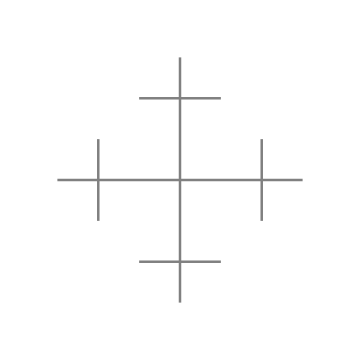

```mathematica
Module[
{
xStep=1,
yStep=1,
offset=0.5,
lineWidth=0.001,
gridThc=0.005,
hlThc=0.008,
squareGridFunc,
hlFunc,
hlPathFunc
},
(
betheGridFunc[]:=(
{
Gray,Thickness[gridThc],
Line[{{-1.5,0},{1.5,0}}],
Line[{{0,-1.5},{0,1.5}}],
Line[{{1,-0.5},{1,0.5}}],
Line[{{-1,-0.5},{-1,0.5}}],
Line[{{-0.5,1},{0.5,1}}],
Line[{{-0.5,-1},{0.5,-1}}]

}//Flatten
);

bgFun[{xc_,yc_},{w_,h_},col_]:={col,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};

hlFunc[s_,e_,col_,ah_:0.06]:=(
{col,Thickness[hlThc],Arrowheads[ah],Arrow[{s,e}]}
);

(*magnon[{xc_,yc_},{w_,h_}]:={EdgeForm[Thick],Lighter[Red],Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]/2]};
hole[{xc_,yc_},{w_,h_},edge_]:={EdgeForm[Directive[Thick,edge]],LightGray,Rectangle[{xc-w,yc-h},{xc+w,yc+h},RoundingRadius->Sqrt[w*h]]};*)

phases=Show[Graphics[
{
betheGridFunc[],


Inset[MaTeX["r = 0",Magnification->2],Scaled[{0.65,0.53}]],
Inset[MaTeX["r = 1",Magnification->2],Scaled[{0.59,0.66}]],
Inset[MaTeX["r = 2",Magnification->2],Scaled[{0.35,0.46}]],
Inset[MaTeX["r = 3",Magnification->2],Scaled[{0.59,0.34}]],

Inset[MaTeX["m = 0",Magnification->2],Scaled[{0.9,0.53}]],
Inset[MaTeX["m = 1",Magnification->2],Scaled[{0.88,0.66}]],
Inset[MaTeX["m = 2",Magnification->2],Scaled[{0.88,0.34}]],

Inset[MaTeX["m = 0",Magnification->2],Scaled[{0.6,0.92}]],
Inset[MaTeX["m = 1",Magnification->2],Scaled[{0.34,0.81}]],
Inset[MaTeX["m = 2",Magnification->2],Scaled[{0.65,0.81}]],

Inset[MaTeX["m = 0",Magnification->2],Scaled[{0.1,0.53}]],
Inset[MaTeX["m = 2",Magnification->2],Scaled[{0.12,0.66}]],
Inset[MaTeX["m = 1",Magnification->2],Scaled[{0.12,0.34}]],

Inset[MaTeX["m = 0",Magnification->2],Scaled[{0.6,0.08}]],
Inset[MaTeX["m = 2",Magnification->2],Scaled[{0.34,0.18}]],
Inset[MaTeX["m = 1",Magnification->2],Scaled[{0.65,0.18}]]

},
Frame->False,
PlotRange->{{-1.8,1.8},{-1.8,1.8}},
PlotRangeClipping->True
],ImageSize->Medium]
)];
phases
```

```mathematica
Export["phases.png",phases,ImageResolution->300]
```

phases.png